```mathematica
(*Plotting the lineshape against exp and histrogram*)
(*Run solefp-analysis.nb and experimental LS first*)
(*Import *-ftir data*)
SetDirectory["/Users/Sherina/Desktop"];
compHistogram=l105n1 ;
compLS=Import["holo.cam-l105c-n.1-15ns-ftir.dat","Table"][[;;,1;;2]];
expLS=l105exp;
```

```mathematica
(*Plots*)
(*Scaling factor for exp. absorbance*)
expscale=0.051;
(*Scaling factor for calculated absorbance*)
compscale=0.041;
(*Systematic error correction*)
error=0;
(*Axis style option: True: has right frame; Flase: no right frame*)
frameOpt=False;

expLSPlot=Partition[Riffle[expLS[[;;,1]]+error,expLS[[;;,3]]*expscale],2];
compLSPlot=Partition[Riffle[compLS[[;;,1]],compLS[[;;,2]]*compscale],2];
```

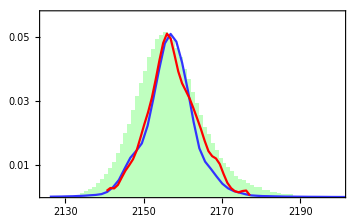

```mathematica
Show[Histogram[Sort[compHistogram][[850;;-870]],{1},"Probability",PlotRange->{{2125,2200},Automatic},ChartStyle->Lighter[Green,0.75],ChartBaseStyle->EdgeForm[None]],ListPlot[compLSPlot[[428;;492]],Joined-> True,PlotRange->{{2125,2220},All},PlotStyle->Lighter[Blue,0.2]],ListPlot[expLSPlot,Joined-> True,PlotStyle->Red],PlotRange-> {{2125,2200},{0.001,0.057}},Frame-> {{True,frameOpt},{True,False}},FrameStyle-> Directive[Black,FontSize-> 16,Thickness-> 0.005],FrameTicks-> {{Table[i,{i,0.01,0.06,0.01}],Table[i,{i,0,0.06,0.01}]},{Table[i,{i,2130,2210,20}],None}},AxesOrigin-> {2125,0},AspectRatio-> 0.6]
```

```mathematica
Sort[compHistogram][[13;;-4]]
```

{2125.09,2125.29,2125.36,2125.38,2125.4,2125.51,2125.58,2125.7,2125.74,2126.09,2126.11,2126.15,2126.21,2126.55,2126.6,2126.75,2126.75,2126.77,2126.83,2126.94,2126.99,2127.05,249942,2208.96,2208.98,2209.94,2210.16,2210.33,2210.65,2210.65,2210.73,2210.84,2211.53,2211.56,2211.92,2212.32,2213.6,2213.67,2213.82,2215.37,2215.46,2216.03,2216.19,2216.21,2219.48}
 |  |  |  |

```mathematica
compLSPlot[[428]]
```

{2126.1,0.000176102}

```mathematica
compLSPlot[[492]]
```

{2219.94,0.0000341332}